# Algoritmo Metropolis-Hastings (pa la tesis)

```mathematica
Get["/media/storage/ciencia/investigacion/proyecto-ss/adanerick/codigo/CoolTools.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos/usefulFunctions.wl"]
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/"]
```

/media/storage/ciencia/trabajo-con-carlos/tesis

El algoritmo y demás funciones necesarias para su ejecución ya se encuentran en el paquete “Tesis`”, escrito en el archivo usefulFunctions.wl

## Toma de muestras generales (distintas β, δ, p y r_z con N fija)

### Una pequeña prueba de la intuición

La distribución que queremos muestrear la aproximamos como: Exp[-β d(CG[ρ_i], ρ_t)]. Los estados ρ_i se obtienen con evoluciones GUE, cuyo “tamaño” o “paso” depende del parámetro δ. Veamos rápido el comportamiento de la exponencial.

```mathematica
betas = {0.1, 1, 10, 100};
```

```mathematica
curves = Exp[-# x]& /@ betas
```

{ⅇ^(-0.1 x),ⅇ^-x,ⅇ^(-10 x),ⅇ^(-100 x)}

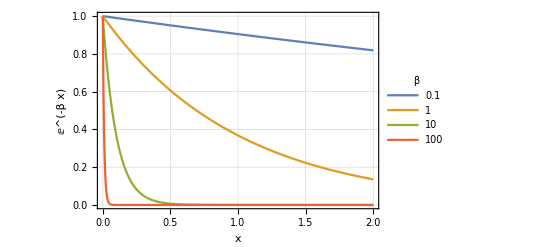

```mathematica
exps = Plot[curves,{x,0,2}, PlotLegends->LineLegend[betas, LegendLabel->"β", LegendFunction->(Framed[#, RoundingRadius->5, FrameStyle->Black]&), LabelStyle->Black], 
			FrameLabel->{x,Exp[-β x]},PlotTheme->"Detailed", FrameStyle->Black]
```

```mathematica
Export["many_exponentials.pdf",exps]
```

many_exponentials.pdf

De la gráfica se ve que, entre más grande sea β, menos error sería tolerado para los estados que aspiren a pertenecer a la muestra. Esto significa que debe existir una relación entre el parámetro β y el error del algoritmo ϵ. ¿Cuál es?

### Generación de muchas muestras con distintos valores de parámetros

```mathematica
(*Redefinamos los valores que probaremos:*)
betas ={10, 50, 100, 250, 500, 750, 1000};
deltas = {0.001, 0.003, 0.005, 0.007, 0.009, 0.01, 0.015, 0.02, 0.025, 0.03, 0.035, 0.04, 0.045, 0.05, 0.055, 0.06, 0.065, 0.07, 0.075, 0.08, 0.085, 0.09};
rzs = {0, 0.5, 0.8};
swapPs = {0.3, 0.5, 0.8};
```

```mathematica
(*Definimos los estados objetivo apropiadamente:*)
targets = (IdentityMatrix[2] + # PauliMatrix[3])/2 & /@ rzs
```

{{{1/2,0},{0,1/2}},{{0.75,0.},{0.,0.25}},{{0.9,0.},{0.,0.1}}}

```mathematica
(*Definimos la mega lista con todos los parámetros que se ejecutarán:*)
allParams = Flatten[Outer[{#1,#2,#3,#4}&, betas, deltas, swapPs, targets,1],3];
```

```mathematica
(*Master loop to follow the overall execution:*)
Do[
	result = Timing[metropolisHastingsSampleTest[8000, universalInitState, allParams[[i]]]];
	filename = "sampleMH_"<>ToString[i]<>".m";
	Export[filename, result];
	Print["Guardada la muestra: "<>ToString[i]],
{i, 1, Length[allParams]}]
(*Guardada la muestra 987. Aquí se quedó en la primera corrida*)
(*En la segunda corrida se comenzará a partir del 991, por lo que faltarán el 988, 989 y 990. Esta corrida se quedó en: Guardada la muestra 1107*)
(*Tercera corrida se reanudará en el 1108, pues la segunda se paró por error. Esta se quedó en: Guardada la muestra 1152*)
(*Cuarta corrida iniciará en 1189, por lo que faltarán el 1153, 1188 y todos lo que estén en medio. Esto corresponde a todas las muestras con β=750 y δ={0.075, 0.08, 0.085 y 0.09}*)
(*La cuarta corrida se quedó en: Guardada la muestra 1282. Falta de la 1283 hasta la 1386*)
```

```mathematica
(*En gral, las muestras que faltan son:*)
(*988, 989, 990, 1153 a 1188, 1283 a 1386*)
```

## Toma de muestras con distintas N (pero β, δ, p y r_z fijas)

```mathematica
SetDirectory["/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/distintasN_beta500_delta0p01"]
```

/media/storage/ciencia/trabajo-con-carlos/tesis/muestras_MH/distintasN_beta500_delta0p01

```mathematica
β = 500;
δ = {0.001, 0.02, 0.05};
rz = 0.5;
swapP = 0.3;
enes = {10000, 30000, 50000, 70000, 90000, 100000, 120000, 150000, 170000, 20000};
```

```mathematica
targets =  ((IdentityMatrix[2] + # PauliMatrix[3])/2)& /@ rzs
```

rzs

### Toma de las muestras para distintas N

```mathematica
initstates = Outer[initStateGenerator[β, δ, #1, #2, 0.01]&, swapPs, targets,1];
```

```mathematica
runAndExportWDistsN[N_, β_, δ_, swapP_, rz_]:= With[{targetstate = (IdentityMatrix[2] + rz PauliMatrix[3])/2},
													With[{initialstate = initStateGenerator[β, δ, swapP, targetstate, 0.01]},
														sample = Timing[metropolisHastingsSample[N, β, δ, swapP, initialstate, targetstate]];
													    Export["MHsample_N="<>ToString[N]<>"_delta="<>ToString[δ]<>"_rz="<>ToString[rz]<>"_p="<>ToString[swapP]<>".wl", sample];
												        Print["Guardada la muestra: "<>"MHsample_N="<>ToString[N]<>"_delta="<>ToString[δ]<>"_rz="<>ToString[rz]<>"_p="<>ToString[swapP]]
													]
									 		 ]
```

```mathematica
runForFixedPAndR[sizes_, β_, δ_, swapP_, rz_]:= runAndExportWDistsN[#, β, δ, swapP, rz]& /@ sizes
```

```mathematica
(*Generación de las muestras:*)
Outer[runForFixedPAndR[enes, β, δ, #1, #2]&, swapPs, rzs]
```

```mathematica
Map[runForFixedPAndR[enes, β, #, swapP, rz]&, δ]
```

Guardada la muestra: MHsample_N=10000_delta=0.001_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=30000_delta=0.001_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=50000_delta=0.001_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=70000_delta=0.001_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=90000_delta=0.001_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=100000_delta=0.001_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=120000_delta=0.001_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=150000_delta=0.001_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=170000_delta=0.001_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=20000_delta=0.001_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=10000_delta=0.02_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=30000_delta=0.02_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=50000_delta=0.02_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=70000_delta=0.02_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=90000_delta=0.02_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=100000_delta=0.02_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=120000_delta=0.02_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=150000_delta=0.02_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=170000_delta=0.02_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=20000_delta=0.02_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=10000_delta=0.05_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=30000_delta=0.05_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=50000_delta=0.05_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=70000_delta=0.05_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=90000_delta=0.05_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=100000_delta=0.05_rz=0.5_p=0.3

Guardada la muestra: MHsample_N=120000_delta=0.05_rz=0.5_p=0.3

$Aborted